Do Figure 3b using the Barbosa expression, the Liemohn and Khazanov [1998]–derived expression, and my own NIntegrate thing

## Set up functions

### Helpers

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

### Liemohn and Khazanov Maxwellian and kappa funcs (LKMwellDensFac and LKKappaDensFac)

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

### Barbosa Maxwellian and kappa funcs (BarbosawellDensFac and BarbosaKappaDensFac)

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Barbosa_funcs.wl
```

#### Some plots of the Barbosa Funcs

```mathematica
Plot[BarbosaKappaDensFac[941/110,RB,3],{RB,1,100}]
```

$Aborted

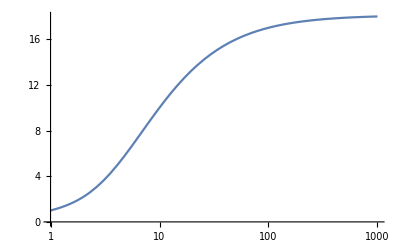

```mathematica
LogLinearPlot[BarbosaMwellDensFac[941/110,RB],{RB,1,1000}]
```

### My own ‘nilla

```mathematica
MaxwellArbPotCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
KappaArbPotCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
SpenceMaxwellDensFac[phiBar_,RB_]:=NIntegrate[rho^2 Sin[phi] MaxwellArbPotCylUnitStep[rho,phi,√phiBar,1/RB],{rho,phiBar/2,phiBar*2},{phi,0,π/2}]
SpenceKappaDensFac[phiBar_,RB_,kappa_]:=NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,√phiBar,1/RB,kappa],{rho,phiBar/3,phiBar*3},{phi,0,π/2}]
```

## Define functions for mapping density back to FAST

```mathematica
funkerMaxwell[densFac_,Tm_,Kmeas_]:=Kmeas/preFactor * √Tm *densFac;
```

```mathematica
funkerKappa[densFac_,Tm_,Kmeas_,κ_]:=Kmeas/preFactor * √Tm *densFac*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
dPhi = 941;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

## Plot options

```mathematica
kappas={155/100,16/10,175/100,201/100,245/100,401/100,10};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

Part::partw: Part 8 of {31/20,8/5,7/4,201/100,49/20,401/100,10} does not exist.

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 31/20,κ = 8/5,κ = 7/4,κ = 201/100,κ = κ_t (≃ 2.45),κ = 401/100,κ = 10,κ = {31/20,8/5,7/4,201/100,49/20,401/100,10}⟦8⟧}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

## PLOHT

#### PICK RB VALUE UP FRONT---SpenceMaxwellDensFac will want it

```mathematica
RB=20
```

#### Get SpenceMaxwellFunc values

```mathematica
(*plotTms={1,2,3,5,7,10,20,30,50,70,100,200,300,500,700,1000};*)
```

```mathematica
(*SpenceMaxwells = Table[{Tm,SpenceMaxwellDensFac[dPhi/Tm,RB]},{Tm,plotTms}]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.18559,1.20782}. NIntegrate obtained 4.19041 and 0.0000110139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {0.995219,1.55549}. NIntegrate obtained 3.2507 and 0.0000122416 for the integral and error estimates.

{{1,0.},{2,1.11661},{3,14.3583},{5,14.5159},{7,14.6877},{10,14.9836},{20,16.3197},{30,17.4487},{50,17.808},{70,16.8446},{100,14.927},{200,10.244},{300,7.74251},{500,5.36268},{700,4.19041},{1000,3.2507}}

```mathematica
SpenceMaxwells={{1,0.},{2,1.116605015777176},{3,14.35827819359595},{5,14.515927874910217},{7,14.68771308846283},{10,14.983571307175888},{20,16.31969044860193},{30,17.448689313749796},{50,17.808032961674975},{70,16.844605517848652},{100,14.926978885771241},{200,10.24395777114994},{300,7.742509279923568},{500,5.3626824537099305},{700,4.190408476940789},{1000,3.2507044166620584}}
```

{{1,0.},{2,1.11661},{3,14.3583},{5,14.5159},{7,14.6877},{10,14.9836},{20,16.3197},{30,17.4487},{50,17.808},{70,16.8446},{100,14.927},{200,10.244},{300,7.74251},{500,5.36268},{700,4.19041},{1000,3.2507}}

#### Get SpenceMaxwellFunc values

```mathematica
plotTms={1,2,3,5,7,10,20,30,50,70,100,200,300,500,700,1000};
```

```mathematica
(*SpenceKappa2 = Table[{Tm,SpenceKappaDensFac[dPhi/Tm,RB,2]},{Tm,plotTms}]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
SpenceKappa2 ={{1,1.5641262677357688*^-8},{2,1.5697077607683848*^-7},{3,6.392661155587778*^-7},{5,4.102054385292448*^-6},{7,0.000015123133870383768},{10,0.00006700485898046721},{20,0.002140169805840265},{30,0.03441235143416782},{50,6.328910065794095},{70,15.58862676129876},{100,15.57257738175017},{200,14.012831966778243},{300,12.377814231629234},{500,9.879669995749216},{700,8.195050479133622},{1000,6.501364164994118}};
```

```mathematica
(*SpenceKappa1p8 = Table[{Tm,SpenceKappaDensFac[dPhi/Tm,RB,18/10]},{Tm,plotTms}]*)
```

```mathematica
SpenceKappa1p8 = {{1,8.379894325332977*^-8},{2,6.231544158193489*^-7},{3,2.118117446314051*^-6},{5,0.000010729844645410004},{7,0.000033596859701108284},{10,0.00012398405851867897},{20,0.002646670328934013},{30,0.032100571185225295},{50,5.662309828182467},{70,15.401218330192789},{100,15.529102560736447},{200,14.68800238203452},{300,13.533320324282826},{500,11.436477197172412},{700,9.822919861375787},{1000,8.06272384928148}};
```

### Maxwellian plots

```mathematica
plotRange={{1,999},{0,10}};
```

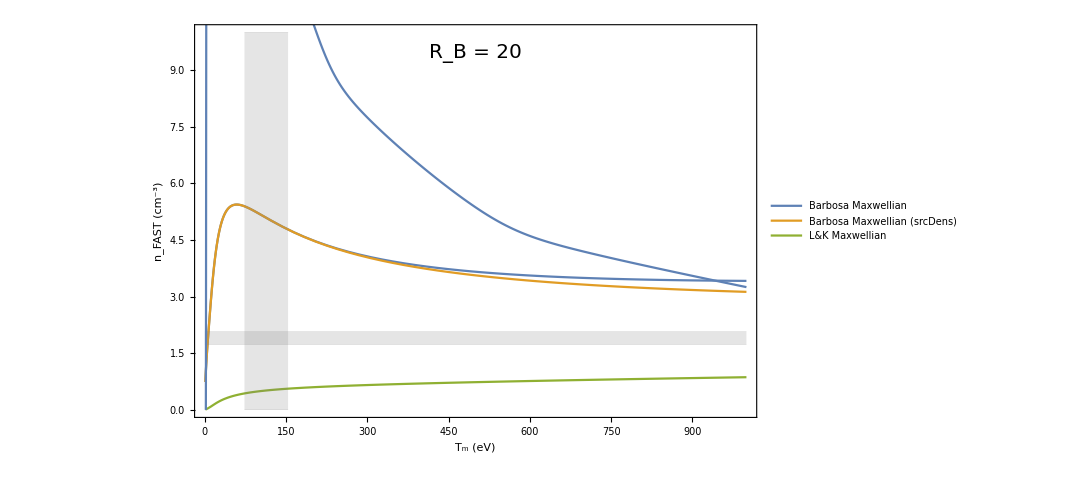

```mathematica
Show[Plot[{funkerMaxwell[BarbosaMwellDensFac[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[BarbosaMwellDensFacSourceNorm[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[LKMwellDensFac[dPhi/Tm,RB],Tm,measCond]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa Maxwellian","Barbosa Maxwellian (srcDens)","L&K Maxwellian"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceMaxwells,Joined->True,InterpolationOrder->3]]
```

### Kappa plots

```mathematica
kappa=2;
```

```mathematica
plotRange={{1,999},{0,10}};
```

Plot::exclul: {Tm-0,(1+2 ((BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]))-0,((√π)/8+√(941/(2 π)) √(1/Tm) (1/(2 Plus[«2»])+(√Tm ArcTan[Times[«2»]])/(2 √1882)))-0,Tm-0,Im[Tm]-0,2 Im[(BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]]-0} must be a list of equalities or real-valued functions.

Plot::exclul: {Tm-0,(1+2 ((BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]))-0,Tm-0,Im[Tm]-0,2 Im[(BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]]-0} must be a list of equalities or real-valued functions.

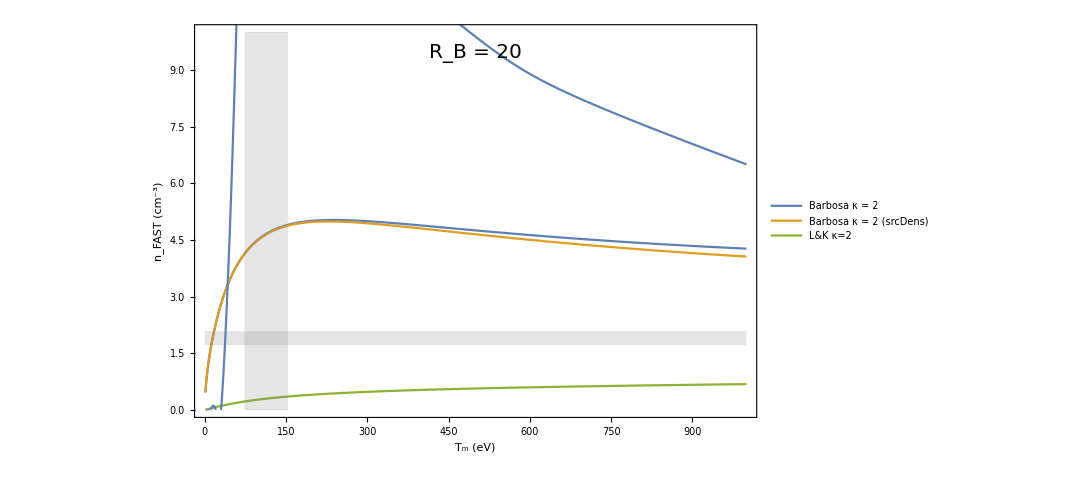

```mathematica
Show[Plot[{funkerKappa[BarbosaKappaDensFac [dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[BarbosaKappaDensFacSourceNorm[dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa κ = 2","Barbosa κ = 2 (srcDens)","L&K κ=2"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceKappa2,Joined->True,InterpolationOrder->3]]
```

```mathematica
kappa=1.8;
```

```mathematica
plotRange={{1,999},{0,10}};
```

Plot::exclul: {Tm-0,-3136.67/Tm-1,(1+3.33333 ((BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]))-0,(0.267663+17.5544 √(1/Tm) Hypergeometric2F1[1/2,1.8,3/2,-3136.67/Tm])-0,Tm-0,Im[Tm]-0,-3136.67 Im[1/Tm]-0,3.33333 Im[(BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]]-0} must be a list of equalities or real-valued functions.

Plot::exclul: {Tm-0,(1+3.33333 ((BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]))-0,Tm-0,Im[Tm]-0,3.33333 Im[(BarbosaFuncs`Private`rho)^2+941/Tm-2 √941 BarbosaFuncs`Private`rho √Power[«2»] √Plus[«2»]]-0} must be a list of equalities or real-valued functions.

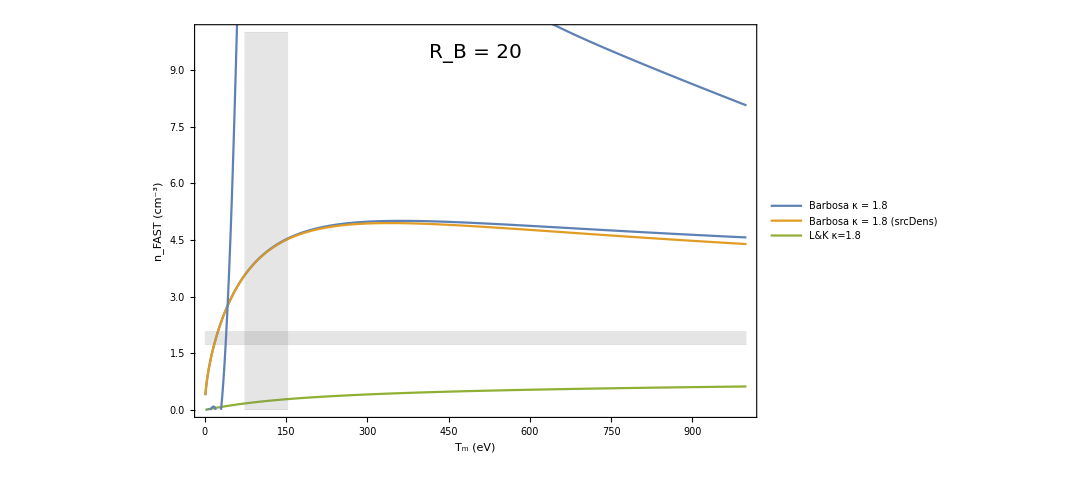

```mathematica
Show[Plot[{funkerKappa[BarbosaKappaDensFac [dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[BarbosaKappaDensFacSourceNorm[dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa κ = 1.8","Barbosa κ = 1.8 (srcDens)","L&K κ=1.8"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceKappa1p8,Joined->True,InterpolationOrder->3]]
```

### Alternative with different density bounds

```mathematica
RB=20;
```

```mathematica
minDens=0.98;
maxDens=1.30;
minT=73.14;
maxT= 153.68;
```

```mathematica
plotRange={{1,999},{0,10}};
```

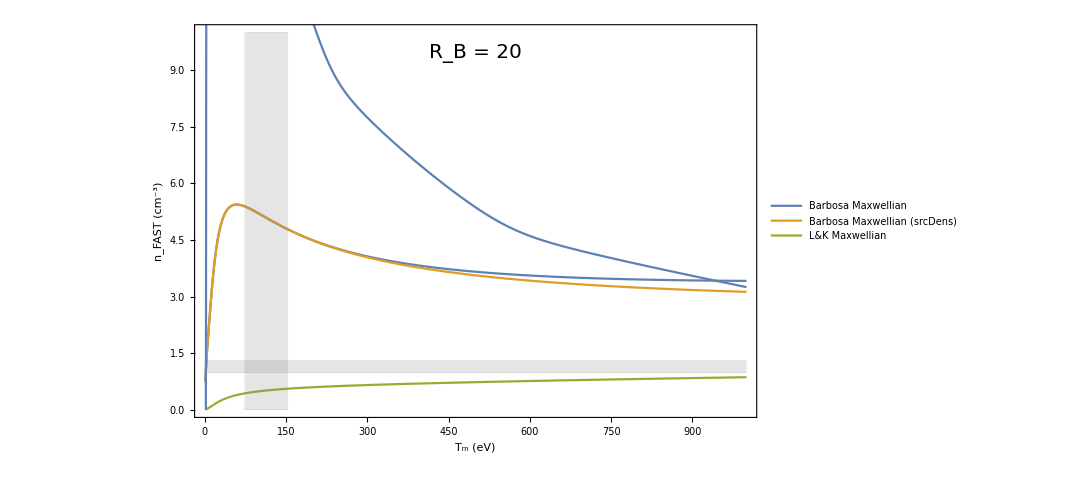

```mathematica
Show[Plot[{funkerMaxwell[BarbosaMwellDensFac[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[BarbosaMwellDensFacSourceNorm[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[LKMwellDensFac[dPhi/Tm,RB],Tm,measCond]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa Maxwellian","Barbosa Maxwellian (srcDens)","L&K Maxwellian"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceMaxwells,Joined->True,InterpolationOrder->3]]
```

```mathematica
kappa=2;
```

```mathematica
plotRange={{1,999},{0,10}};
```

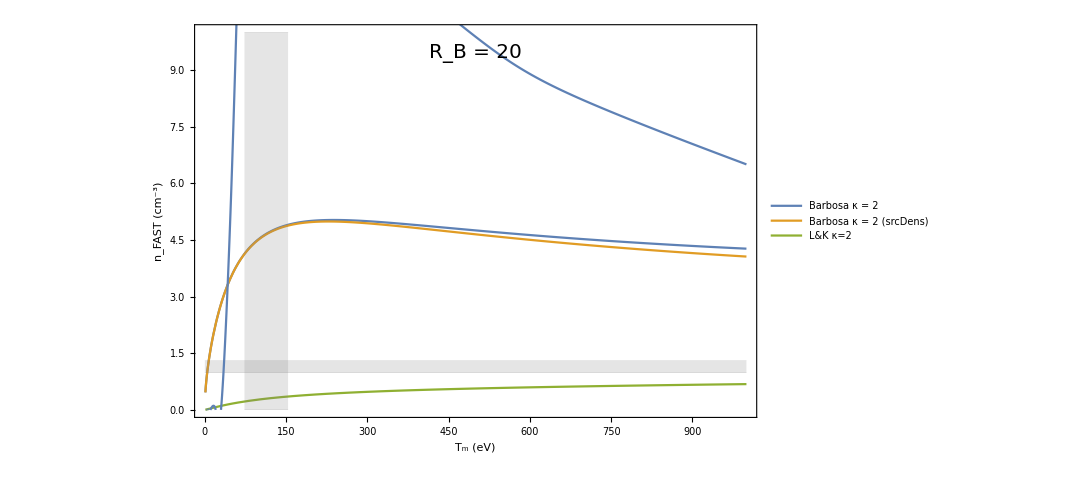

```mathematica
Show[Plot[{funkerKappa[BarbosaKappaDensFac [dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[BarbosaKappaDensFacSourceNorm[dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa κ = 2","Barbosa κ = 2 (srcDens)","L&K κ=2"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceKappa2,Joined->True,InterpolationOrder->3]]
```

### RB=100

```mathematica
RB=100;
```

```mathematica
plotRange={{1,999},{0,10}};
```

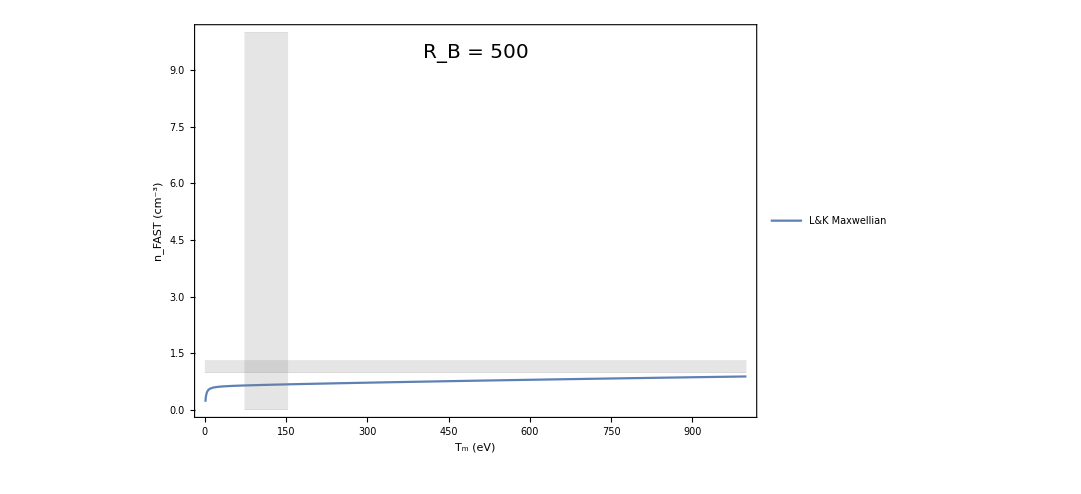

```mathematica
Show[Plot[{funkerMaxwell[LKMwellDensFac[dPhi/Tm,RB],Tm,measCond]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"L&K Maxwellian"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

```mathematica
kappa=201/100;
```

```mathematica
LKKappaDensFac[dPhi/Tm,1000,kappa+0.01]
```

4.38155

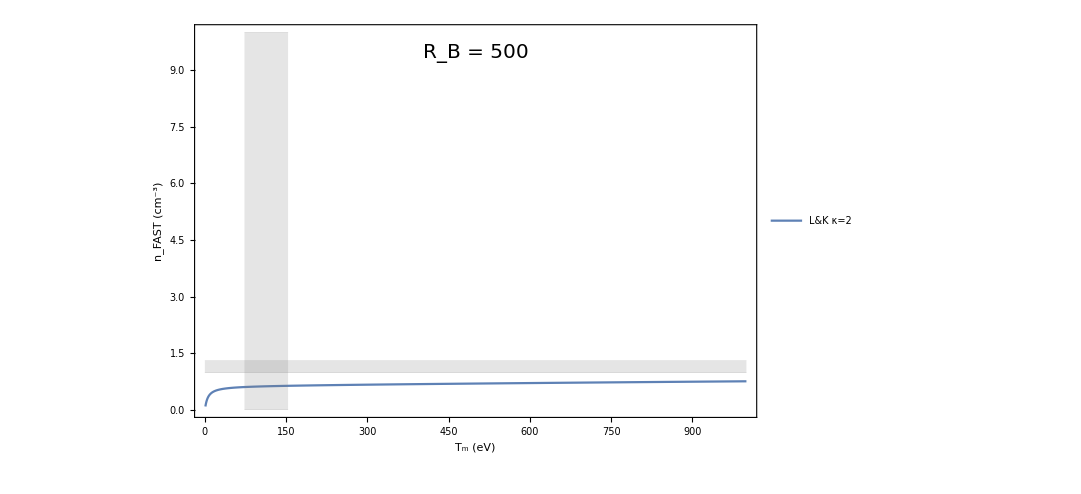

```mathematica
Show[Plot[{funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"L&K κ=2"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

```mathematica
RB=500;
```

```mathematica
kappa=1.6;
```

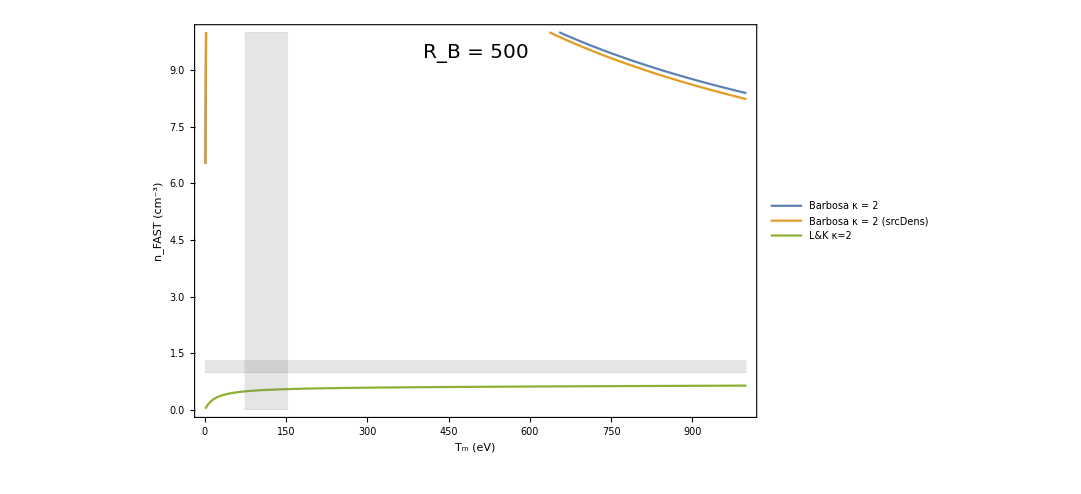

```mathematica
Show[Plot[{funkerKappa[BarbosaKappaDensFac [dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[BarbosaKappaDensFacSourceNorm[dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa κ = 2","Barbosa κ = 2 (srcDens)","L&K κ=2"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

#### Get SpenceMaxwellFunc values

```mathematica
plotTms={1,2,3,5,7,10,20,30,50,70,100,200,300,500,700,1000};
```

```mathematica
SpenceMaxwells = Table[{Tm,SpenceMaxwellDensFac[dPhi/Tm,RB]},{Tm,plotTms}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {0.974914,1.5553071280897292523459629620674604666419327259063720703125}. NIntegrate obtained 1.83813 and 2.97155×10^-6 for the integral and error estimates.

{{1,0.},{2,0.},{3,0.},{5,0.},{7,0.},{10,0.},{20,3.72393×10^-106},{30,2.1973×10^-35},{50,8.32636×10^-7},{70,0.179506},{100,8.48868},{200,13.1741},{300,9.30361},{500,5.97077},{700,3.98543},{1000,1.83813}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

### Maxwellian plots

```mathematica
plotRange={{1,999},{0,10}};
```

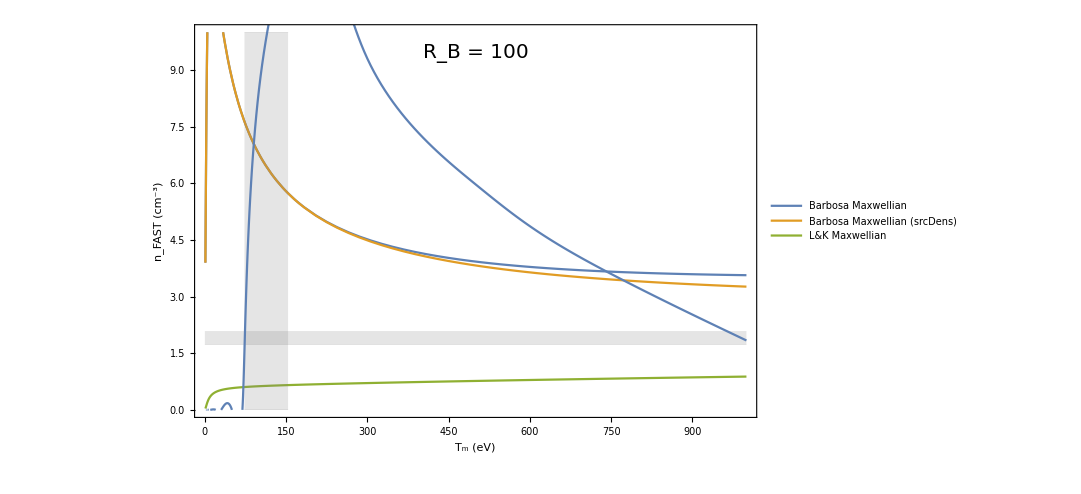

```mathematica
Show[Plot[{funkerMaxwell[BarbosaMwellDensFac[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[BarbosaMwellDensFacSourceNorm[dPhi/Tm,RB],Tm,measCond],funkerMaxwell[LKMwellDensFac[dPhi/Tm,RB],Tm,measCond]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa Maxwellian","Barbosa Maxwellian (srcDens)","L&K Maxwellian"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]],ListPlot[SpenceMaxwells,Joined->True,InterpolationOrder->3]]
```

```mathematica
kappa=1.6
```

1.6

```mathematica
RB=1000
```

1000

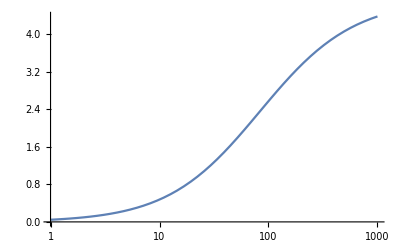

```mathematica
LogLinearPlot[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],{RB,1,1000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

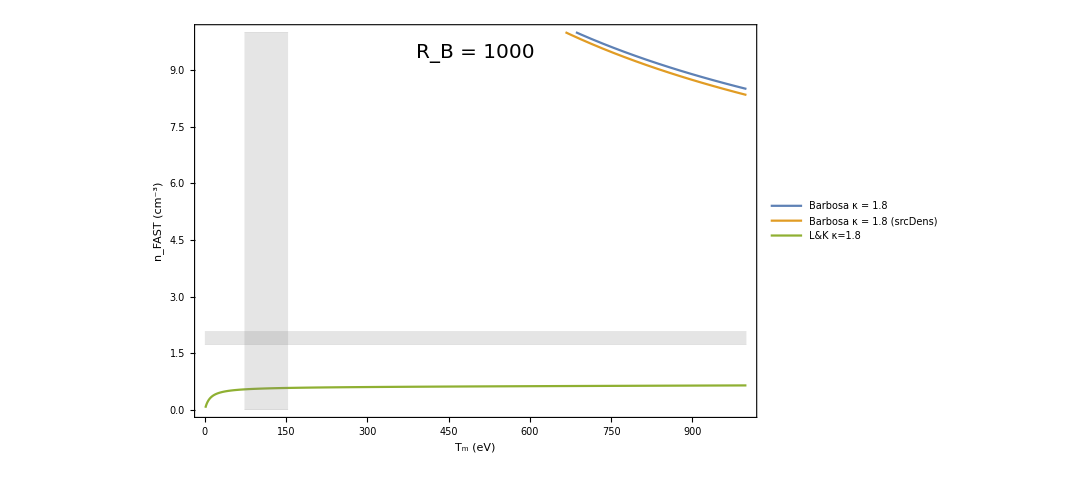

```mathematica
Show[Plot[{funkerKappa[BarbosaKappaDensFac [dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[BarbosaKappaDensFacSourceNorm[dPhi/Tm,RB,kappa],Tm,measCond,kappa],funkerKappa[LKKappaDensFac[dPhi/Tm,RB,kappa+0.01],Tm,measCond,kappa]},{Tm,1,1000},PlotRange->plotRange,LabelStyle->(FontSize->16),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,18],ImageSize->800,Epilog->{Text[Style[StringForm["R_B = `1`",RB],20],Scaled[{0.5,0.95}],{0,1}]},PlotLegends->{"Barbosa κ = 1.8","Barbosa κ = 1.8 (srcDens)","L&K κ=1.8"}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

### No labels, handle manually

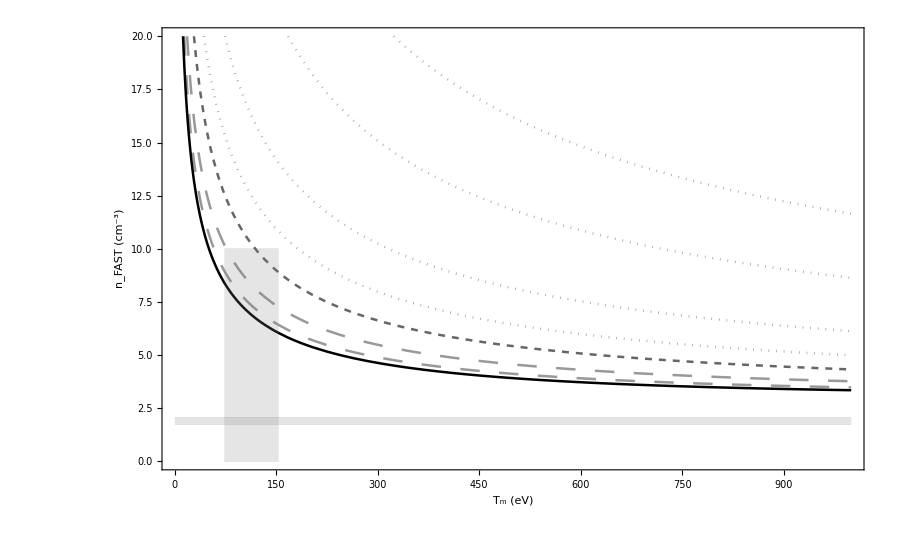

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,20}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

## Just Maxwellian (resized)

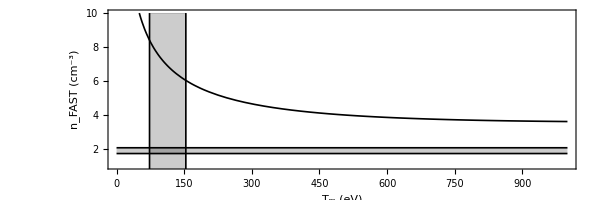

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{1,10}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->{600,300},AspectRatio->1/3],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}},{{minT,0},{minT,10}},{{maxT,0},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->{Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]]}]]
```

## Maxwellian, with suggestive kappa lines

```mathematica
fakeKappa={1.53,1.6};
```

```mathematica
fakeStyles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]]};
```

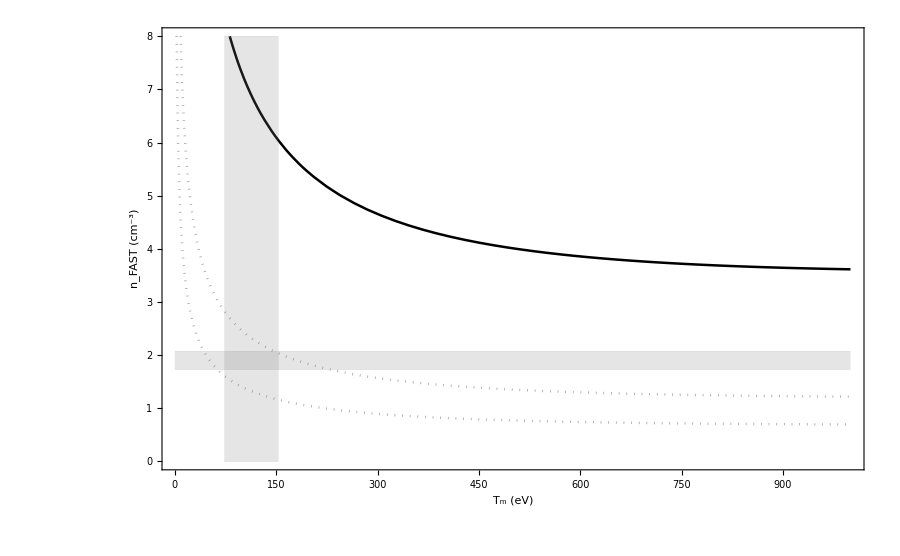

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],Table[Plot[funkerFake[Ep,Tm,fakeKappa[[k]],measCond],{Tm,1,1000},PlotStyle->fakeStyles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,8},{maxT,8}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

## Maxwellian, scaled to magnetosphere properly (not bogus Barbosa density)

```mathematica
fakeKappa={1.53,1.6};
```

```mathematica
fakeStyles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]]};
```

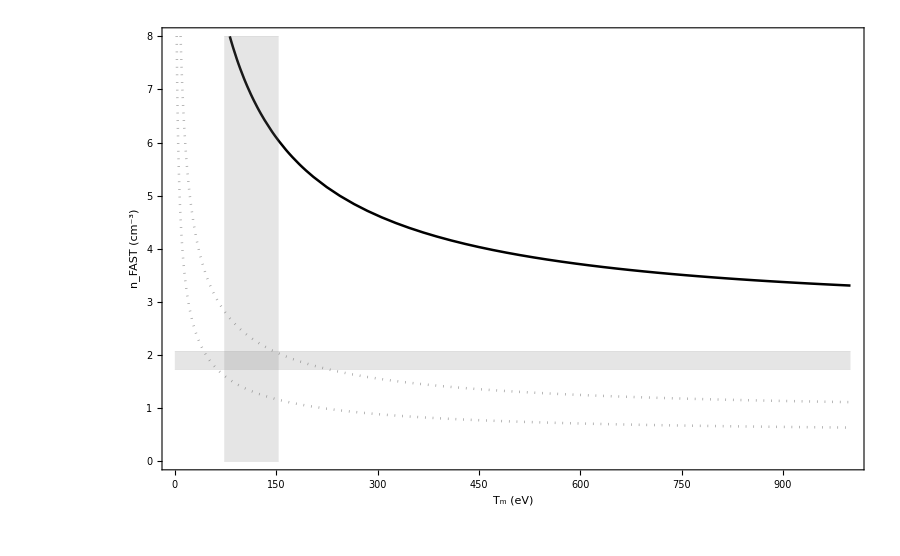

```mathematica
Show[Plot[funkerBarb2[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],Table[Plot[funkerFake2[Ep,Tm,fakeKappa[[k]],measCond],{Tm,1,1000},PlotStyle->fakeStyles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,8},{maxT,8}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```